```mathematica
Fr[θ_,α_]:=Fn[α]*Cos[α-θ]-Ft[α]*Sin[α-θ]
```

```mathematica
Fs[θ_,α_]:=Fn[α]*Sin[α-θ]+Ft[α]*Cos[α-θ]
```

```mathematica
Fn[α_]:=p*A*Abs[Cos[α]]*Cos[α](1+ϵ)
```

```mathematica
Ft[α_]:=p*A*(1-ϵ)*Abs[Cos[α]]*Sin[α]
```

```mathematica
f=Transpose[{
vr[t],
vs[t]/r[t],
(-vr[t]*vs[t])/r[t]+Fs[θ[t],α[t]]/m,
vs[t]^2/r[t]-μ/r[t]^2+Fr[θ[t],α[t]]/m
}];
```

```mathematica
Grad[f,{r[t],θ[t],vs[t],vr[t]}]//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 1
-vs[t]/r[t]^2 | 0 | 1/r[t] | 0
(vr[t] vs[t])/r[t]^2 | -(A p Abs[Cos[α[t]]] (Cos[2 α[t]-θ[t]]+ϵ Cos[θ[t]]))/m | -vr[t]/r[t] | -vs[t]/r[t]
(2 μ-r[t] vs[t]^2)/r[t]^3 | (A p Abs[Cos[α[t]]] (Sin[2 α[t]-θ[t]]-ϵ Sin[θ[t]]))/m | (2 vs[t])/r[t] | 0)

```mathematica
λRHS=Dot[{λr[t],λθ[t],λvs[t],λvr[t]},Grad[f,{r[t],θ[t],vs[t],vr[t]}]]//FullSimplify;
```

```mathematica
αexpr=Assuming[{m>0,A>0,p>0,-π/2<α[t],π/2>α[t],ϵ>0,ϵ<1},FullSimplify[(D[Dot[Transpose[{λt[t],λθ[t],λvs[t],λvr[t]}],f],α[t]])==0]]
```

(2+ϵ+3 Cos[2 α[t]]) Cos[θ[t]] Sin[α[t]] λvr[t]==1/2 ((Cos[α[t]]+3 Cos[3 α[t]]) Cos[θ[t]] λvs[t]+Sin[θ[t]] ((Cos[α[t]]+3 Cos[3 α[t]]) λvr[t]+2 (2+ϵ+3 Cos[2 α[t]]) Sin[α[t]] λvs[t]))

Here we write down all the equations for the system (We have 9 unknowns, so we need 9 equations)

```mathematica
eqPropagation=MapThread[#1==#2&,{{r'[t],θ'[t],vs'[t],vr'[t]},f}];
eqLambda=MapThread[#1==#2&,{{λr'[t],λθ'[t],λvs'[t],λvr'[t]},λRHS}];
eqControl={αexpr};
```

```mathematica
eqs=Join[eqPropagation, eqLambda, eqControl];
```

We can drop the λθ equation, as both initial and ending condition are zero and it doesn’t appear in the other dynamics, so we assume it to be zero.

```mathematica
(*eqs=eqs[[{1,2,3,4,5,7,8,9}]];*)
```

```mathematica
eqs//TableForm
```

r'[t]==vr[t]
θ'[t]==vs[t]/r[t]
vs'[t]==(A p (1-ϵ) Abs[Cos[α[t]]] Cos[α[t]-θ[t]] Sin[α[t]]+A p (1+ϵ) Abs[Cos[α[t]]] Cos[α[t]] Sin[α[t]-θ[t]])/m-(vr[t] vs[t])/r[t]
vr'[t]==-μ/r[t]^2+(A p (1+ϵ) Abs[Cos[α[t]]] Cos[α[t]] Cos[α[t]-θ[t]]-A p (1-ϵ) Abs[Cos[α[t]]] Sin[α[t]] Sin[α[t]-θ[t]])/m+vs[t]^2/r[t]
λr'[t]==((2 μ-r[t] vs[t]^2) λvr[t]+r[t] vs[t] (vr[t] λvs[t]-λθ[t]))/r[t]^3
λθ'[t]==-(A p Abs[Cos[α[t]]] ((-Sin[2 α[t]-θ[t]]+ϵ Sin[θ[t]]) λvr[t]+(Cos[2 α[t]-θ[t]]+ϵ Cos[θ[t]]) λvs[t]))/m
λvs'[t]==(2 vs[t] λvr[t]-vr[t] λvs[t]+λθ[t])/r[t]
λvr'[t]==λr[t]-(vs[t] λvs[t])/r[t]
(2+ϵ+3 Cos[2 α[t]]) Cos[θ[t]] Sin[α[t]] λvr[t]==1/2 ((Cos[α[t]]+3 Cos[3 α[t]]) Cos[θ[t]] λvs[t]+Sin[θ[t]] ((Cos[α[t]]+3 Cos[3 α[t]]) λvr[t]+2 (2+ϵ+3 Cos[2 α[t]]) Sin[α[t]] λvs[t]))

Here we write down the initial conditions

```mathematica
constants={
A->1(*m.b2*),
p->1 (*Momentum flux of incoming light per unit area (THINK!)*),
m->10 (*kg*),
μ->3.986004418*10^14 (*m.b3/s.b2*),
ϵ->0.6,
r0->7000*10^3,
tf->10000};
```

```mathematica
circularInitialConditions={
θ[0]==0,
r[0]==r0,
vs[0]==Sqrt[μ/r0],
vr[0]==0
};
```

```mathematica
(*Returns λ[tf](desired)-λ[tf](assuming λ0), to be used with FindRoot*)
```

```mathematica
SolveSystem[eqs_,initialConditions_,lambda_,constants_]:=Block[
{centralLambdaConditions,simplifyAbs,systemCentral,slnCentral,desiredLambda,ϕ},
simplifyAbs={Abs[x_]->Sqrt[x^2]};
centralLambdaConditions={
λr[0]==lambda[[1]],
λθ[0]==lambda[[2]],
λvs[0]==lambda[[3]],
λvr[0]==lambda[[4]]
};
systemCentral=Join[eqs,initialConditions,centralLambdaConditions]/.constants/.simplifyAbs;
NDSolveValue[systemCentral,{r[t],θ[t],vs[t],vr[t],α[t],λr[t],λθ[t],λvs[t],λvr[t]},{t,0,tf}/.constants,WorkingPrecision->MachinePrecision,PrecisionGoal->3]
];
```

```mathematica
FinalLambdaError[eqs_, initialConditions_,lambda_/;VectorQ[lambda,NumericQ],constants_ ]:=Block[
{slnCentral,desiredLambda,ϕ},
slnCentral=SolveSystem[eqs,initialConditions,lambda,constants];
ϕ[t_]:=1/2*(vr[t]^2+(r[t]*vs[t])2)-μ/r[t];
desiredLambda={
D[ϕ[tf],r[tf]],
D[ϕ[tf],θ[tf]],
D[ϕ[tf],vs[tf]],
D[ϕ[tf],vr[tf]]
}/.{r[tf]->slnCentral[[1]],θ[tf]->slnCentral[[2]],vs[tf]->slnCentral[[3]],vr[tf]->slnCentral[[4]]}/.t->tf/.constants;
(desiredLambda-{slnCentral[[6]],slnCentral[[7]],slnCentral[[8]],slnCentral[[9]]}/.t->tf/.constants)
];
```

```mathematica
monitoredFindRoot[args__]:=Module[{s=0,e=0,j=0},{FindRoot[args,StepMonitor:>s++,EvaluationMonitor:>e++,Jacobian->{Automatic,EvaluationMonitor:>j++}],"Steps"->s,"Evaluations"->e,"Jacobian Evaluations"->j}]
```

```mathematica
(*Initial conditions, must be reasonable otherwise the root search fails miserably*)
```

```mathematica
root={λrv->2400,λθv->-65400,λvsv->4324,λvrv->5454};
```

```mathematica
(*Execute the following block as many times as desired to refine solution*)
```

NDSolveValue::ndcf: Repeated convergence test failure at t == 7687.51; unable to continue.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

{λrv→2384.88,λθv→-723506.,λvsv→8882.4,λvrv→5326.7}

Desired λr = 7785.05, calculated = -8277.42

Desired λθ = 0, calculated = 1.23836×10^9

Desired λvs = 6.38845×10^6, calculated = -4.78203×10^6

Desired λvr = 1371.99, calculated = -847811.

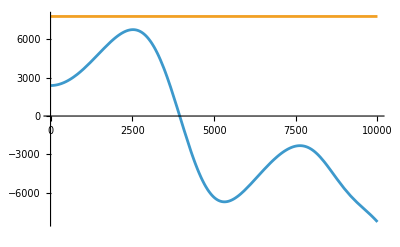

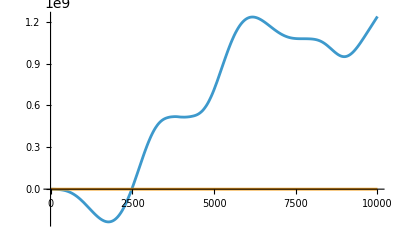

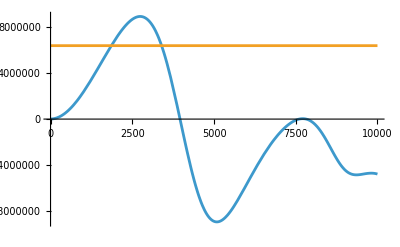

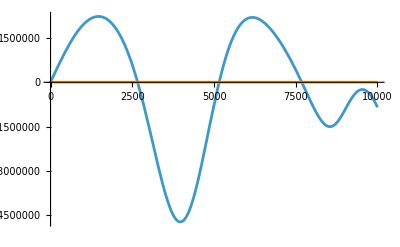

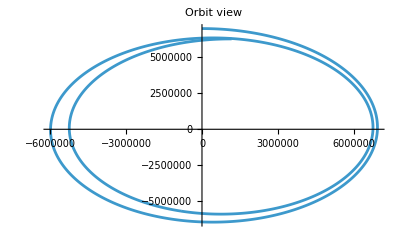

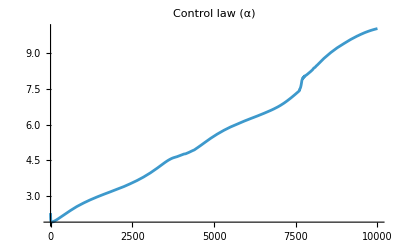

```mathematica
Block[
{},
root=FindRoot[FinalLambdaError[eqs,circularInitialConditions,{λrv,λθv,λvsv,λvrv},constants],{{λrv,λrv/.root},{λθv,λθv/.root},{λvsv,λvsv/.root},{λvrv,λvrv/.root}},MaxIterations->1,Method->"Automatic",WorkingPrecision->MachinePrecision];
Print[root];
sln=SolveSystem[eqs,circularInitialConditions,{λrv,λθv,λvsv,λvrv}/.root,constants];
ϕ[t_]:=1/2*(vr[t]^2+(r[t]*vs[t])2)-μ/r[t];
desiredLambda={
D[ϕ[tf],r[tf]],
D[ϕ[tf],θ[tf]],
D[ϕ[tf],vs[tf]],
D[ϕ[tf],vr[tf]]
}/.{r[tf]->sln[[1]],θ[tf]->sln[[2]],vs[tf]->sln[[3]],vr[tf]->sln[[4]]}/.t->tf/.constants;
Print["Desired λr = ",desiredLambda[[1]],", calculated = ",sln[[6]]/.t->tf/.constants];
Print["Desired λθ = ",desiredLambda[[2]],", calculated = ",sln[[7]]/.t->tf/.constants];
Print["Desired λvs = ",desiredLambda[[3]],", calculated = ",sln[[8]]/.t->tf/.constants];
Print["Desired λvr = ",desiredLambda[[4]],", calculated = ",sln[[9]]/.t->tf/.constants];
Print[Plot[{sln[[6]],desiredLambda[[1]]},{t,0,tf}/.constants]];
Print[Plot[{sln[[7]],desiredLambda[[2]]},{t,0,tf}/.constants]];
Print[Plot[{sln[[8]],desiredLambda[[3]]},{t,0,tf}/.constants]];
Print[Plot[{sln[[9]],desiredLambda[[4]]},{t,0,tf}/.constants]];
points=Table[{sln[[1]]*Sin[sln[[2]]],sln[[1]]*Cos[sln[[2]]]},({t,0,tf/.constants,1})];
Print[ListLinePlot[points,PlotLabel->"Orbit view"]];
Print[Plot[sln[[5]],{t,0,tf}/.constants,PlotLabel->"Control law (α)"]]
]
```

```mathematica
P
```

P